```mathematica
Needs["VariationalMethods`"]
```

```mathematica
f[u_,uh_,z_,θ_,μ_]:=1-(u/uh)^(2+z-θ)+μ^2(z-θ)/2/(2-θ)u^(2z-2θ+2)/uh^(2z-2θ)(1-(u/uh)^(θ-z))
```

```mathematica
EulerEquations[q μ (1-(u[t]/uh)^(z-θ))-u[t]^(θ/2-1)Sqrt[u[t]^(2-2z)f[u[t],uh,z,θ,μ]-u'[t]^2/f[u[t],uh,z,θ,μ]],u[t],t]
```

-(q (z-θ) μ (u[t]/uh)^(z-θ))/u[t]-((-2+θ) u[t]^(-2+θ/2) u'[t]^2)/(2 (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))) √(u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))))+(u[t]^(θ/2) (-2 (-2+θ) (-2-z+θ) (u[t]/uh)^(z-θ)+uh^(2-2 z+2 θ) (z-θ)^2 μ^2 u[t]^(2 (z-θ)) (u[t]/uh)^(-z+θ)+2 uh^(2-2 z+2 θ) (z-θ) (1+z-θ) μ^2 u[t]^(2 (z-θ)) (1-(u[t]/uh)^(-z+θ))) u'[t]^2)/(2 uh^2 (2-θ) (-1+(u[t]/uh)^(2+z-θ)-(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))^2 √(u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))))-1/2 (-2+θ) u[t]^(-2+θ/2) √(u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))))-(u[t]^(-1+θ/2) ((2-2 z) u[t]^(1-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))+1/(2 uh^2 (2-θ))u[t]^3 (-2 (-2+θ) (-2-z+θ) u[t]^(-2 z) (u[t]/uh)^(z-θ)+uh^(2-2 z+2 θ) (z-θ)^2 μ^2 u[t]^(-2 θ) (u[t]/uh)^(-z+θ)+2 uh^(2-2 z+2 θ) (z-θ) (1+z-θ) μ^2 u[t]^(-2 θ) (1-(u[t]/uh)^(-z+θ)))+(u[t] (-2 (-2+θ) (-2-z+θ) (u[t]/uh)^(z-θ)+uh^(2-2 z+2 θ) (z-θ)^2 μ^2 u[t]^(2 (z-θ)) (u[t]/uh)^(-z+θ)+2 uh^(2-2 z+2 θ) (z-θ) (1+z-θ) μ^2 u[t]^(2 (z-θ)) (1-(u[t]/uh)^(-z+θ))) u'[t]^2)/(2 uh^2 (2-θ) (-1+(u[t]/uh)^(2+z-θ)-(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))^2)))/(2 √(u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))))-(u[t]^(-1+θ/2) u''[t])/((1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))) √(u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))))+(u[t]^(-1+θ/2) u'[t] ((2-2 z) u[t]^(1-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))) u'[t]+1/(2 uh^2 (2-θ))u[t]^3 (-2 (-2+θ) (-2-z+θ) u[t]^(-2 z) (u[t]/uh)^(z-θ)+uh^(2-2 z+2 θ) (z-θ)^2 μ^2 u[t]^(-2 θ) (u[t]/uh)^(-z+θ)+2 uh^(2-2 z+2 θ) (z-θ) (1+z-θ) μ^2 u[t]^(-2 θ) (1-(u[t]/uh)^(-z+θ))) u'[t]+(u[t] (-2 (-2+θ) (-2-z+θ) (u[t]/uh)^(z-θ)+uh^(2-2 z+2 θ) (z-θ)^2 μ^2 u[t]^(2 (z-θ)) (u[t]/uh)^(-z+θ)+2 uh^(2-2 z+2 θ) (z-θ) (1+z-θ) μ^2 u[t]^(2 (z-θ)) (1-(u[t]/uh)^(-z+θ))) u'[t]^3)/(2 uh^2 (2-θ) (-1+(u[t]/uh)^(2+z-θ)-(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))^2)-(2 u'[t] u''[t])/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))))/(2 (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))) (u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))))^(3/2))==0

```mathematica
Reduce[(0≤θ≤2(z-1)&&1≤z<2)||(0≤θ<2&&z≥2),{θ,z}]
```

0≤θ<2&&z≥(2+θ)/2

```mathematica
Reduce[(0≤θ≤2(z-1)&&1≤z<2)||(0≤θ<2&&z≥2),{z,θ}]
```

(z==1&&θ==0)||(1<z<2&&0≤θ≤-2+2 z)||(z≥2&&0≤θ<2)

```mathematica
qcrit[us_,uh_,z_,θ_,μ_]:=us^(θ/2-z)Sqrt[f[us,uh,z,θ,μ]]/μ/(1-(us/uh)^(z-θ));
μext[uh_,z_,θ_]:=Sqrt[2(2-θ)(2+z-θ)]/(z-θ)/uh;
```

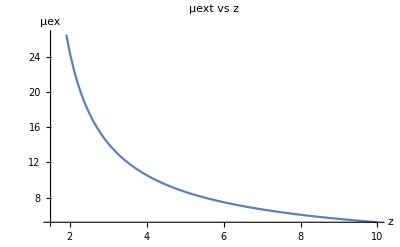

```mathematica
Plot[μext[0.1,z,1],{z,1.5,10},PlotLabel->"μext vs z",AxesLabel->{z,μex}]
```

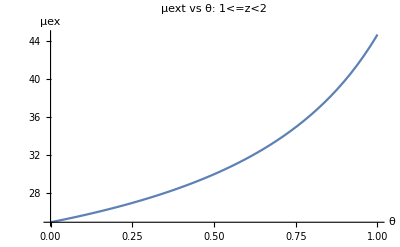

```mathematica
Plot[μext[0.1,1.5,θ],{θ,0,1},PlotLabel->"μext vs θ: 1<=z<2",AxesLabel->{θ,μex}]
```

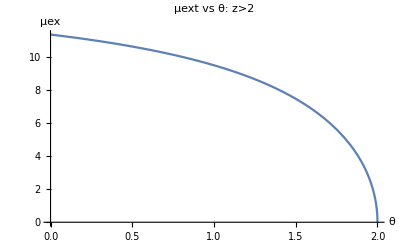

```mathematica
Plot[μext[0.1,4.5,θ],{θ,0,2},PlotLabel->"μext vs θ: z>2",AxesLabel->{θ,μex}]
```

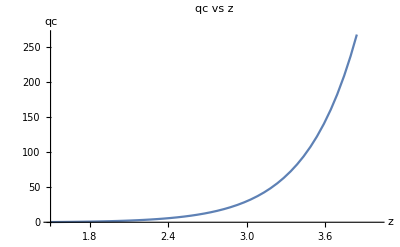

```mathematica
Plot[qcrit[0.1,1,z,1,0.75μext[0.1,z,1]],{z,1.5,4},PlotLabel->"qc vs z",AxesLabel->{z,qc}]
```

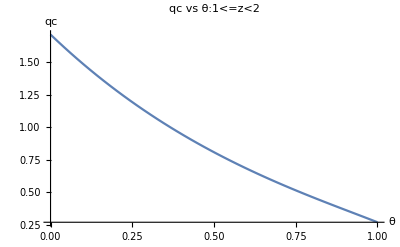

```mathematica
Plot[qcrit[0.1,1,1.5,θ,0.75μext[0.1,1.5,θ]],{θ,0,1},PlotLabel->"qc vs θ:1<=z<2",AxesLabel->{θ,qc}]
```

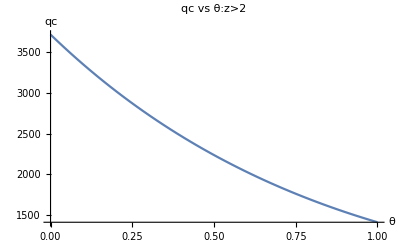

```mathematica
Plot[qcrit[0.1,1,4.5,θ,0.75μext[0.1,4.5,θ]],{θ,0,1},PlotLabel->"qc vs θ:z>2",AxesLabel->{θ,qc}]
```

```mathematica
ut[us_,uh_,z_,θ_,μ_,q_]:=NDSolveValue[{-(q (z-θ) μ (u[t]/uh)^(z-θ))/u[t]-((-2+θ) u[t]^(-2+θ/2) u'[t]^2)/(2 (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))) √(u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))))+(u[t]^(θ/2) (-2 (-2+θ) (-2-z+θ) (u[t]/uh)^(z-θ)+uh^(2-2 z+2 θ) (z-θ)^2 μ^2 u[t]^(2 (z-θ)) (u[t]/uh)^(-z+θ)+2 uh^(2-2 z+2 θ) (z-θ) (1+z-θ) μ^2 u[t]^(2 (z-θ)) (1-(u[t]/uh)^(-z+θ))) u'[t]^2)/(2 uh^2 (2-θ) (-1+(u[t]/uh)^(2+z-θ)-(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))^2 √(u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))))-1/2 (-2+θ) u[t]^(-2+θ/2) √(u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))))-(u[t]^(-1+θ/2) ((2-2 z) u[t]^(1-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))+1/(2 uh^2 (2-θ))u[t]^3 (-2 (-2+θ) (-2-z+θ) u[t]^(-2 z) (u[t]/uh)^(z-θ)+uh^(2-2 z+2 θ) (z-θ)^2 μ^2 u[t]^(-2 θ) (u[t]/uh)^(-z+θ)+2 uh^(2-2 z+2 θ) (z-θ) (1+z-θ) μ^2 u[t]^(-2 θ) (1-(u[t]/uh)^(-z+θ)))+(u[t] (-2 (-2+θ) (-2-z+θ) (u[t]/uh)^(z-θ)+uh^(2-2 z+2 θ) (z-θ)^2 μ^2 u[t]^(2 (z-θ)) (u[t]/uh)^(-z+θ)+2 uh^(2-2 z+2 θ) (z-θ) (1+z-θ) μ^2 u[t]^(2 (z-θ)) (1-(u[t]/uh)^(-z+θ))) u'[t]^2)/(2 uh^2 (2-θ) (-1+(u[t]/uh)^(2+z-θ)-(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))^2)))/(2 √(u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))))-(u[t]^(-1+θ/2) u''[t])/((1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))) √(u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))))+(u[t]^(-1+θ/2) u'[t] ((2-2 z) u[t]^(1-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))) u'[t]+1/(2 uh^2 (2-θ))u[t]^3 (-2 (-2+θ) (-2-z+θ) u[t]^(-2 z) (u[t]/uh)^(z-θ)+uh^(2-2 z+2 θ) (z-θ)^2 μ^2 u[t]^(-2 θ) (u[t]/uh)^(-z+θ)+2 uh^(2-2 z+2 θ) (z-θ) (1+z-θ) μ^2 u[t]^(-2 θ) (1-(u[t]/uh)^(-z+θ))) u'[t]+(u[t] (-2 (-2+θ) (-2-z+θ) (u[t]/uh)^(z-θ)+uh^(2-2 z+2 θ) (z-θ)^2 μ^2 u[t]^(2 (z-θ)) (u[t]/uh)^(-z+θ)+2 uh^(2-2 z+2 θ) (z-θ) (1+z-θ) μ^2 u[t]^(2 (z-θ)) (1-(u[t]/uh)^(-z+θ))) u'[t]^3)/(2 uh^2 (2-θ) (-1+(u[t]/uh)^(2+z-θ)-(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))^2)-(2 u'[t] u''[t])/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))))/(2 (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))) (u[t]^(2-2 z) (1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ)))-u'[t]^2/(1-(u[t]/uh)^(2+z-θ)+(uh^(-2 z+2 θ) (z-θ) μ^2 u[t]^(2+2 z-2 θ) (1-(u[t]/uh)^(-z+θ)))/(2 (2-θ))))^(3/2))==0,u[0]==us,u'[0]==0},u,{t,0.01,5},Method->"BDF"];
ut1[t1_,us_,uh_,z_,θ_,μ_,q_]:=ut[us,uh,z,θ,μ,q][t1];
ut[0.1,1,1.5,0.5,0.75μext[1,1.5,0.5],qcrit[0.1,1,1.5,0.5,0.75μext[1,1.5,0.5]]][0.5]
ut1[0.5,0.1,1,1.5,0.5,0.75μext[1,1.5,0.5],qcrit[0.1,1,1.5,0.5,0.75μext[1,1.5,0.5]]]
```

0.685807

0.685807

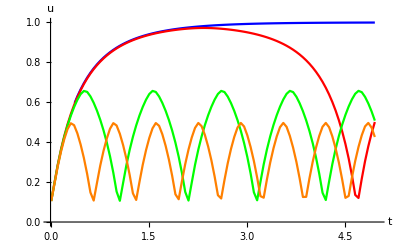

```mathematica
Show[
ListLinePlot[Table[{i,ut1[i,0.1,1,1.5,0.5,0.75μext[1,1.5,0.5],0.5qcrit[0.1,1,1.5,0.5,0.75μext[1,1.5,0.5]]]//Abs},{i,0.01,5,0.05}],PlotStyle->Blue],
ListLinePlot[Table[{i,ut1[i,0.1,1,1.5,0.5,0.75μext[1,1.5,0.5],1.02qcrit[0.1,1,1.5,0.5,0.75μext[1,1.5,0.5]]]//Abs},{i,0.01,5,0.05}],PlotStyle->Red],
ListLinePlot[Table[{i,ut1[i,0.1,1,1.5,0.5,0.75μext[1,1.5,0.5],1.5qcrit[0.1,1,1.5,0.5,0.75μext[1,1.5,0.5]]]//Abs},{i,0.01,5,0.05}],PlotStyle->Green],
ListLinePlot[Table[{i,ut1[i,0.1,1,1.5,0.5,0.75μext[1,1.5,0.5],2.0qcrit[0.1,1,1.5,0.5,0.75μext[1,1.5,0.5]]]//Abs},{i,0.01,5,0.05}],PlotStyle->Orange],AxesOrigin->{0,0},AxesLabel->{t,u},PlotRange->{{0,5},{0,1}}
]
```

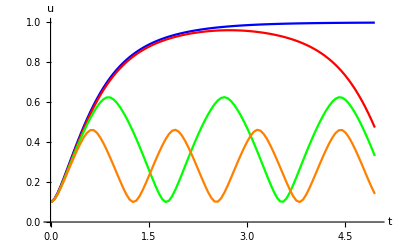

```mathematica
Show[
ListLinePlot[Table[{i,ut1[i,0.1,1,1.0,0.0,0.75μext[1,1.0,0.0],0.5qcrit[0.1,1,1.0,0.0,0.75μext[1,1.0,0.0]]]//Abs},{i,0.01,5,0.05}],PlotStyle->Blue],
ListLinePlot[Table[{i,ut1[i,0.1,1,1.0,0.0,0.75μext[1,1.0,0.0],1.02qcrit[0.1,1,1.0,0.0,0.75μext[1,1.0,0.0]]]//Abs},{i,0.01,5,0.05}],PlotStyle->Red],
ListLinePlot[Table[{i,ut1[i,0.1,1,1.0,0.0,0.75μext[1,1.0,0.0],1.5qcrit[0.1,1,1.0,0.0,0.75μext[1,1.0,0.0]]]//Abs},{i,0.01,5,0.05}],PlotStyle->Green],
ListLinePlot[Table[{i,ut1[i,0.1,1,1.0,0.0,0.75μext[1,1.0,0.0],2.0qcrit[0.1,1,1.0,0.0,0.75μext[1,1.0,0.0]]]//Abs},{i,0.01,5,0.05}],PlotStyle->Orange],AxesOrigin->{0,0},AxesLabel->{t,u},PlotRange->{{0,5},{0,1}}
]
```

```mathematica
D[1-(u/uh)^(2+z-θ)+μ^2(z-θ)/2/(2-θ)u^(2z-2θ+2)/uh^(2z-2θ)(1-(u/uh)^(θ-z)),u]//FullSimplify//InputForm
```

(u*(u/uh)^(z - θ)*(-2 - z + θ))/uh^2 + (u^(1 + 2*z - 2*θ)*uh^(-2*z + 2*θ)*(-z + θ)*(2*(u/uh)^z*(1 + z - θ) + (u/uh)^θ*(-2 - z + θ))*μ^2)/
  (2*(u/uh)^z*(-2 + θ))

```mathematica
dfu[t1_,us_,uh_,z_,θ_,μ_,q_]:=D[ut[us,uh,z,θ,μ,q][t],t]/.{t->t1};
pu[t1_,us_,uh_,z_,θ_,μ_,q_]:=ut1[t1,us,uh,z,θ,μ,q]^(θ/2-1)dfu[t1,us,uh,z,θ,μ,q]/Sqrt[ut1[t1,us,uh,z,θ,μ,q]^(2-2z)f[ut1[t1,us,uh,z,θ,μ,q],uh,z,θ,μ]^3-dfu[t1,us,uh,z,θ,μ,q]^2f[ut1[t1,us,uh,z,θ,μ,q],uh,z,θ,μ]];
βpu[t1_,us_,uh_,z_,θ_,μ_,q_]:=pu[t1,us,uh,z,θ,μ,q]/((ut1[t1,us,uh,z,θ,μ,q]*(ut1[t1,us,uh,z,θ,μ,q]/uh)^(z-θ)*(-2-z+θ))/uh^2+(ut1[t1,us,uh,z,θ,μ,q]^(1+2*z-2*θ)*uh^(-2*z+2*θ)*(-z+θ)*(2*(ut1[t1,us,uh,z,θ,μ,q]/uh)^z*(1+z-θ)+(ut1[t1,us,uh,z,θ,μ,q]/uh)^θ*(-2-z+θ))*μ^2)/(2*(ut1[t1,us,uh,z,θ,μ,q]/uh)^z*(-2+θ)));
```

```mathematica
Table[{i,pu[i,0.1,1,1.5,0.5,0.75μext[1,1.5,0.5],0.5qcrit[0.1,1,1.5,0.5,0.75μext[1,1.5,0.5]]]},{i,0.01,5,0.05}]
```

{{0.01,2.02879},{0.06,6.83015},{0.11,8.6592},{0.16,9.97582},{0.21,11.1801},{0.26,12.4012},{0.31,13.6967},{0.36,15.0986},{0.41,16.627},{0.46,18.2969},{0.51,20.1206},{0.56,22.1097},{0.61,24.2741},{0.66,26.6263},{0.71,29.1764},{0.76,31.9373},{0.81,34.9191},{0.86,38.136},{0.91,41.6034},{0.96,45.3355},{1.01,49.353},{1.06,53.6685},{1.11,58.3033},{1.16,63.2766},{1.21,68.6047},{1.26,74.3316},{1.31,80.4661},{1.36,87.0039},{1.41,94.0119},{1.46,101.557},{1.51,109.552},{1.56,118.226},{1.61,127.298},{1.66,137.245},{1.71,147.71},{1.76,158.945},{1.81,171.078},{1.86,183.691},{1.91,197.314},{1.96,212.23},{2.01,227.989},{2.06,244.42},{2.11,261.896},{2.16,280.82},{2.21,301.262},{2.26,323.224},{2.31,346.059},{2.36,370.287},{2.41,396.626},{2.46,425.109},{2.51,455.354},{2.56,487.302},{2.61,518.933},{2.66,554.892},{2.71,598.464},{2.76,644.924},{2.81,688.352},{2.86,731.183},{2.91,777.149},{2.96,824.043},{3.01,900.167},{3.06,956.649},{3.11,992.791},{3.16,1078.68},{3.21,1187.42},{3.26,1243.22},{3.31,1298.25},{3.36,1405.18},{3.41,1508.41},{3.46,1468.12},{3.51,1761.21},{3.56,1719.07},{3.61,1831.1},{3.66,2192.46},{3.71,2062.11},{3.76,2328.5},{3.81,2577.29},{3.86,2267.56},{3.91,3055.52},{3.96,2329.13},{4.01,3568.49},{4.06,2594.39},{4.11,3928.57},{4.16,3081.07},{4.21,4158.85},{4.26,3660.58},{4.31,4228.47},{4.36,4302.7},{4.41,3839.55},{4.46,3674.99},{4.51,4612.58},{4.56,3132.38},{4.61,7086.48},{4.66,3177.11},{4.71,10328.5},{4.76,3717.41},{4.81,8131.05},{4.86,5672.37},{4.91,14394.7},{4.96,9261.67}}

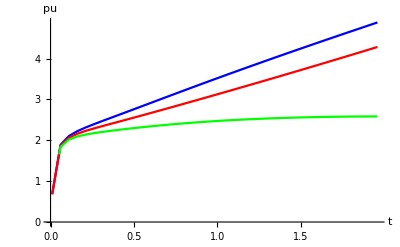

```mathematica
Show[
ListLinePlot[Table[{i,pu[i,0.1,1,1.5,0.5,0.75μext[1,1.5,0.5],0.70qcrit[0.1,1,1.5,0.5,0.75μext[1,1.5,0.5]]]//Abs//Log},{i,0.01,2,0.05}],PlotStyle->Blue],
ListLinePlot[Table[{i,pu[i,0.1,1,1.5,0.5,0.75μext[1,1.5,0.5],0.85qcrit[0.1,1,1.5,0.5,0.75μext[1,1.5,0.5]]]//Abs//Log},{i,0.01,2,0.05}],PlotStyle->Red],
ListLinePlot[Table[{i,pu[i,0.1,1,1.5,0.5,0.75μext[1,1.5,0.5],1.00qcrit[0.1,1,1.5,0.5,0.75μext[1,1.5,0.5]]]//Abs//Log},{i,0.01,2,0.05}],PlotStyle->Green]
,AxesOrigin->{0,0},AxesLabel->{t,pu}
]
```

```mathematica
Table[{i,βpu[i,0.1,1,1.5,0.5,0.75μext[1,1.5,0.5],0.5qcrit[0.1,1,1.5,0.5,0.75μext[1,1.5,0.5]]]},{i,0.01,5,0.05}]
```

{{0.01,-24.7253},{0.06,-25.7129},{0.11,-16.8527},{0.16,-13.2035},{0.21,-11.5177},{0.26,-10.7568},{0.31,-10.5219},{0.36,-10.6337},{0.41,-11.003},{0.46,-11.583},{0.51,-12.3491},{0.56,-13.2891},{0.61,-14.3975},{0.66,-15.6752},{0.71,-17.1247},{0.76,-18.7523},{0.81,-20.5638},{0.86,-22.5686},{0.91,-24.7773},{0.96,-27.2005},{1.01,-29.8532},{1.06,-32.7455},{1.11,-35.8934},{1.16,-39.3117},{1.21,-43.0137},{1.26,-47.0299},{1.31,-51.3695},{1.36,-56.0326},{1.41,-61.0655},{1.46,-66.5152},{1.51,-72.328},{1.56,-78.6579},{1.61,-85.3228},{1.66,-92.6432},{1.71,-100.384},{1.76,-108.72},{1.81,-117.741},{1.86,-127.162},{1.91,-137.354},{1.96,-148.518},{2.01,-160.345},{2.06,-172.715},{2.11,-185.893},{2.16,-200.17},{2.21,-215.6},{2.26,-232.191},{2.31,-249.48},{2.36,-267.842},{2.41,-287.803},{2.46,-309.39},{2.51,-332.332},{2.56,-356.588},{2.61,-380.677},{2.66,-408.008},{2.71,-441.013},{2.76,-476.231},{2.81,-509.286},{2.86,-541.962},{2.91,-577.019},{2.96,-612.822},{3.01,-670.444},{3.06,-713.523},{3.11,-741.465},{3.16,-806.614},{3.21,-888.975},{3.26,-931.769},{3.31,-974.019},{3.36,-1055.26},{3.41,-1133.82},{3.46,-1104.47},{3.51,-1326.02},{3.56,-1295.26},{3.61,-1380.64},{3.66,-1654.19},{3.71,-1556.8},{3.76,-1758.93},{3.81,-1947.92},{3.86,-1714.7},{3.91,-2311.64},{3.96,-1762.88},{4.01,-2702.06},{4.06,-1965.25},{4.11,-2976.97},{4.16,-2335.56},{4.21,-3153.57},{4.26,-2776.58},{4.31,-3208.23},{4.36,-3265.42},{4.41,-2914.65},{4.46,-2790.38},{4.51,-3503.04},{4.56,-2379.39},{4.61,-5383.99},{4.66,-2414.25},{4.71,-7849.83},{4.76,-2825.74},{4.81,-6181.63},{4.86,-4313.01},{4.91,-10946.5},{4.96,-7043.92}}

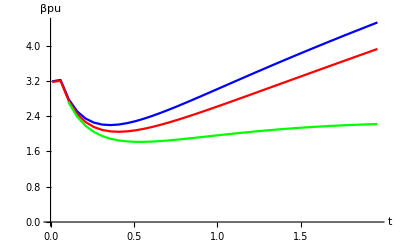

```mathematica
Show[
ListLinePlot[Table[{i,βpu[i,0.1,1,1.5,0.5,0.75μext[1,1.5,0.5],0.70qcrit[0.1,1,1.5,0.5,0.75μext[1,1.5,0.5]]]//Abs//Log},{i,0.01,2,0.05}],PlotStyle->Blue],
ListLinePlot[Table[{i,βpu[i,0.1,1,1.5,0.5,0.75μext[1,1.5,0.5],0.85qcrit[0.1,1,1.5,0.5,0.75μext[1,1.5,0.5]]]//Abs//Log},{i,0.01,2,0.05}],PlotStyle->Red],
ListLinePlot[Table[{i,βpu[i,0.1,1,1.5,0.5,0.75μext[1,1.5,0.5],1.00qcrit[0.1,1,1.5,0.5,0.75μext[1,1.5,0.5]]]//Abs//Log},{i,0.01,2,0.05}],PlotStyle->Green]
,AxesOrigin->{0,0},AxesLabel->{t,βpu}
]
```

```mathematica
(*t_,q_,us_,uh_,μ_,z_,θ_*)
```

```mathematica
Table[{i,βpu[i,10,0.1,1,0.75μext[1,1.5389,1.0],1.5389,1.0]//Abs//Log},{i,0.1,5,0.05}]
```

$Aborted

```mathematica
Table[{i,βpu[i,0.1,1,1.5389,1.0,0.75μext[1,1.5389,1.0],10]//Abs//Log},{i,0.01,2,0.05}]
```

{{0.01,1.10456},{0.06,1.56017},{0.11,0.979188},{0.16,0.217024},{0.21,-1.91429},{0.26,-0.0946095},{0.31,0.789359},{0.36,1.40755},{0.41,1.66954},{0.46,1.68671},{0.51,1.39199},{0.56,0.770184},{0.61,-0.12939},{0.66,-1.73697},{0.71,0.243584},{0.76,0.996878},{0.81,1.57384},{0.86,0.975786},{0.91,1.70891},{0.96,1.20936},{1.01,0.539303},{1.06,-0.622496},{1.11,-0.685315},{1.16,0.515044},{1.21,1.19091},{1.26,1.70081},{1.31,0.798524},{1.36,1.5887},{1.41,1.01641},{1.46,0.272497},{1.51,-1.57089},{1.56,-0.169254},{1.61,0.748694},{1.66,1.37458},{1.71,1.70166},{1.76,1.64576},{1.81,1.4247},{1.86,0.810464},{1.91,-0.0571389},{1.96,-2.1566}}

```mathematica
(*t1_,us_,uh_,z_,θ_,μ_,q_*)
```

```mathematica
FindRoot[
10==qcrit[0.1,1,z,1,0.75μext[1,z,1]],{z,1.5389}
]
```

{z→1.77817}

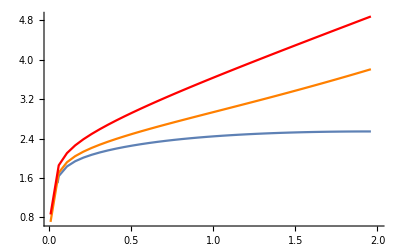

```mathematica
Show[
ListLinePlot[Table[{i,pu[i,0.1,1,1.7782,1.0,0.75μext[1,1.7782,1.0],10]//Abs//Log},{i,0.01,2,0.05}]],
ListLinePlot[Table[{i,pu[i,0.1,1,1.8000,1.0,0.75μext[1,1.8000,1.0],10]//Abs//Log},{i,0.01,2,0.05}],PlotStyle->Orange],
ListLinePlot[Table[{i,pu[i,0.1,1,1.8500,1.0,0.75μext[1,1.8500,1.0],10]//Abs//Log},{i,0.01,2,0.05}],PlotStyle->Red],
PlotRange->{{0.01,2},All},AxesOrigin->{0,0}
]
```

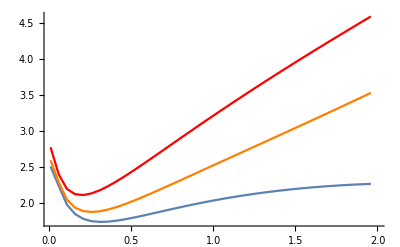

```mathematica
Show[
ListLinePlot[Table[{i,βpu[i,0.1,1,1.7782,1.0,0.75μext[1,1.7782,1.0],10]//Abs//Log},{i,0.01,2,0.05}]],
ListLinePlot[Table[{i,βpu[i,0.1,1,1.8000,1.0,0.75μext[1,1.8000,1.0],10]//Abs//Log},{i,0.01,2,0.05}],PlotStyle->Orange],
ListLinePlot[Table[{i,βpu[i,0.1,1,1.8500,1.0,0.75μext[1,1.8500,1.0],10]//Abs//Log},{i,0.01,2,0.05}],PlotStyle->Red],
PlotRange->{{0.01,2},All},AxesOrigin->{0,0}
]
```

```mathematica
FindRoot[
10==qcrit[0.1,1,1.5,θ,0.75μext[1,1.5,θ]],{θ,0.5}
]
```

{θ→0.405953}

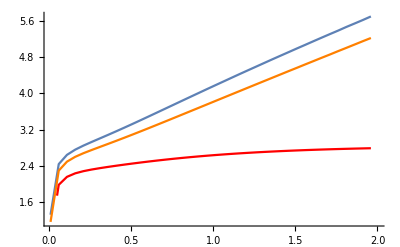

```mathematica
Show[
ListLinePlot[Table[{i,pu[i,0.1,1,1.5,0.101,0.75μext[1,1.5,0.101],10]//Abs//Log},{i,0.01,2,0.05}]],
ListLinePlot[Table[{i,pu[i,0.1,1,1.5,0.202,0.75μext[1,1.5,0.202],10]//Abs//Log},{i,0.01,2,0.05}],PlotStyle->Orange],
ListLinePlot[Table[{i,pu[i,0.1,1,1.5,0.405,0.75μext[1,1.5,0.405],10]//Abs//Log},{i,0.01,2,0.05}],PlotStyle->Red],
PlotRange->{{0.01,2},All},AxesOrigin->{0,0}
]
```

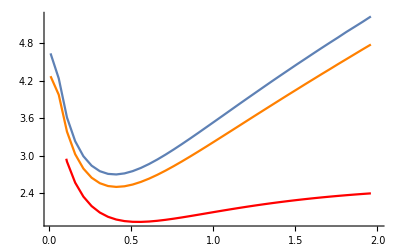

```mathematica
Show[
ListLinePlot[Table[{i,βpu[i,0.1,1,1.5,0.101,0.75μext[1,1.5,0.101],10]//Abs//Log},{i,0.01,2,0.05}]],
ListLinePlot[Table[{i,βpu[i,0.1,1,1.5,0.202,0.75μext[1,1.5,0.202],10]//Abs//Log},{i,0.01,2,0.05}],PlotStyle->Orange],
ListLinePlot[Table[{i,βpu[i,0.1,1,1.5,0.405,0.75μext[1,1.5,0.405],10]//Abs//Log},{i,0.01,2,0.05}],PlotStyle->Red],
PlotRange->{{0.01,2},All},AxesOrigin->{0,0}
]
```